```mathematica
args = {"/Users/baptisteguilleminot/Documents/M2/Stage/data/SDPB_d=6_ci=0_lmax=16_Nmax=20_minmax=max_improv={TH, subTH, SPC}.txt","6","/Users/baptisteguilleminot/Documents/M2/Stage/data/6dMinN20test.mx"};
coeffAmpPath = args[[1]];
d = ToExpression[args[[2]]];
dataPath = args[[3]];
```

## Starting point

```mathematica
Clear[dataAdapt]
dataAdapt=Import[outPath<>"6dMinN20test.mx"]
```

```mathematica
(*Finds the minimums of a function on a grid. Used to initialise the secant method.*)
minPtsFromGraph[data_]:=Module[{pts,coords,vals,nf,k,xmin,xmax,ymin,ymax,margin,interiorQ,mins,depthThreshold,minPts},
pts=data/. {x_,y_,z_}:>{x,y,Log[Abs[z]]};
coords=pts[[All,1;;2]];
vals=pts[[All,3]];

nf=Nearest[coords->Range[Length[coords]]];
k=15;
xmin=Min[coords[[All,1]]];
xmax=Max[coords[[All,1]]];
ymin=Min[coords[[All,2]]];
ymax=Max[coords[[All,2]]];

margin=0.21;
interiorQ[{x_,y_}]:=xmin+margin<x<xmax-margin&&ymin+margin<y<ymax-margin;
mins=Select[Range[Length[pts]],Function[i,Module[{neigh,v},neigh=DeleteCases[nf[coords[[i]],k],i];
v=vals[[i]];
interiorQ[coords[[i]]]&&AllTrue[vals[[neigh]],#>=v&]]]];

minPts=pts[[mins]];
depthThreshold=0.6;
minPts=Select[minPts,Function[p,Module[{neigh,localVals},localVals=vals[[DeleteCases[nf[p[[1;;2]],k],First@nf[p[[1;;2]],1]]]];
Mean[localVals]-p[[3]]>depthThreshold]]];
minPts]
```

```mathematica
Clear[startPts6d,startPtsComplex];
startPts6d=minPtsFromGraph[dataAdapt[[3]]];
(*Turns the points into complex + add manual conditions to remove non physical points -> need optimisation to run without manual input.*)
startPtsComplex = startPts6d[[;;,1]]+I startPts6d[[;;,2]];
startPtsComplex=Join[(*Select[*)startPtsComplex(*,Re[#]<=6.5&]*)]
```

{-8.501+14.501 ⅈ,-5.001+1.001 ⅈ,-4.501+0.501 ⅈ,-8.751+6.751 ⅈ,-7.251+3.251 ⅈ,-5.751+1.751 ⅈ,10.249+25.751 ⅈ}

```mathematica
startPtsComplex={-5.0009999999999994+1.001 ⅈ,-4.5009999999999994+0.501 ⅈ,27.999000000000002+23.001 ⅈ,-8.501+8.251 ⅈ,-7.2509999999999994+3.751 ⅈ,-6.0009999999999994+1.751 ⅈ}
```

{-5.001+1.001 ⅈ,-4.501+0.501 ⅈ,27.999+23.001 ⅈ,-8.501+8.251 ⅈ,-7.251+3.751 ⅈ,-6.001+1.751 ⅈ}

```mathematica
ListDensityPlot[dataAdapt[[1]]/. {x_,y_,z_}:>{x,y,Log[Abs[z]]},Epilog->{Red,PointSize[0.02],Point[startPts6d[[All,1;;2]]]}]
```

-Graphics-

## Secant algorithm

Use secant method of order 2 for optimised computation (one integral per step). First order method to get 3rd point of initialisation.

```mathematica
Clear[secantOrder2];
secantOrder2[myFunc_,start_,nmax_:100,tol_:10^-10]:=Module[{x0,x1,x2, x3,i,a,b,c},
x0=start;
b=myFunc[x0];
x1 = start+(1+I)10^-4;
c=myFunc[x1];
x2=(x1 b-x0 c)/(b- c);
i=0;

While[a=b;
b=c;
c=myFunc[x2];
Abs[c]>tol&&i<nmax&&(i<8||Abs[b]>Abs[c])&&Abs[x2-start]<5,
i=i+1;
(*Guard against duplicate function values/zero denominators*)If[Abs[a-b]<10^-15||Abs[b-c]<10^-15||Abs[a-c]<10^-15,
x2=x2+(1+I)*10^-5;(*Perturb slightly if stuck*)
c=myFunc[x2];
];

x3=(x0 b c)/((a-b) (a-c))+(x1 a c)/((b-a) (b-c))+(x2 a b)/((c-a) (c-b));
x0=x1;
x1=x2;
x2=x3;
];
If[Abs[x2-start]>5,Print["failed point"];x2=start];
x2];
```

```mathematica
secantOrder2[exprJ[9.8,#]&,27.9404866983315679572+23.0217582428250135111ⅈ,200,10^-10]
```

26.9096+23.2519 ⅈ

```mathematica
trajs={{10,27.9404866983315679572+23.0217582428250135111ⅈ }, {9.9, 27.4232941953923429103+23.1365810470392093188ⅈ},{9.8,26.9112289800615736664+23.2507161733774897148 ⅈ}, {9.7,26.4034490935219728862+23.3689092620529891362 ⅈ},{9.6,25.8955699820308250069+23.4979903127217958329 ⅈ},{9.5,25.3786559178365544349+23.6445856828009329112 ⅈ},{9.4,24.9063309766186951958+23.6804383496889961955 ⅈ},{9.3,24.4145428699609637495+23.7909092124658934107 ⅈ},{9.2,23.9211238876553017768+23.9119777225119203106ⅈ},{9.1,23.4534866619947895229+23.9774646864208407063 ⅈ},{9,22.9774479814417310097+24.080558600052041851ⅈ},{8.9,22.5075893073706868049+24.1609455744041107632 ⅈ},{8.8,22.0415390735074298315+24.2521448348876975287 ⅈ},{8.7,21.5801845393839252393+24.3471254779487616026 ⅈ},{8.6,21.1218880236940271059+24.4527573504405994017 ⅈ},{8.5,20.6686912015426824119+24.5037577870630337884 ⅈ},{8.4,20.2210444111035605665+24.5902507504245344951 ⅈ},{8.3,19.7740025346123658072+24.6584426104010120343 ⅈ},{8.2,19.3350171107077940318+24.7391286394848121292 ⅈ},{8.1,18.8937515787588984349+24.8010589618840760568 ⅈ},{8,18.4603774872673234953+24.8708724792850501992 ⅈ}};
```

```mathematica
Abs[exprJ[9.5,Rationalize[29.3786559178365544349+28.6445856828009329112 ⅈ]]]
```

0.00181951906279645

```mathematica
Abs[exprJ[10,27.7318020244982097859+22.887971860812825469 ⅈ]]
```

0.00002587232456728

```mathematica
trackZeroJplane[myFunc_,start_,smin_,smax_,ds_]:=Module[{root=start},Table[root=secantOrder2[myFunc[#,s+10^-16 I]&,root];
{s,root},{s,smin,smax,ds}]](*Track a zero when increasing s by small step. The roots of previous step is used as starting point for next one.*)
trackZeroSplane[myFunc_,start_,Jmin_,Jmax_,dJ_]:=Module[{root1=start, root2=start},Table[{root1,root2}={root2,secantOrder2[myFunc[JJ,#]&,root1,100,10^-10]};
{JJ,root2},{JJ,Jmin,Jmax,dJ}]]
```

```mathematica
LaunchKernels[Length[startPtsComplex]]
trajs=ParallelTable[trackZeroSplane[exprJ,startPtsComplex[[k]],6,2,-0.1],{k,1,Length[startPtsComplex]}];
CloseKernels[];
```

{Local (5),Local (5),Local (5),Local (5),Local (5)}

```mathematica
trajs
```

{{{6.,-4.98598+0.86976 ⅈ},{5.9,-4.98542+0.867872 ⅈ},{5.8,-4.98486+0.86598 ⅈ},{5.7,-4.9843+0.864087 ⅈ},{5.6,-4.98374+0.86219 ⅈ},{5.5,-4.98318+0.860291 ⅈ},{5.4,-4.98262+0.85839 ⅈ},{5.3,-4.98207+0.856485 ⅈ},{5.2,-4.98152+0.854577 ⅈ},{5.1,-4.98097+0.852665 ⅈ},{5.,-4.98042+0.85075 ⅈ},{4.9,-4.97987+0.848831 ⅈ},{4.8,-4.97932+0.846908 ⅈ},{4.7,-4.97878+0.844981 ⅈ},{4.6,-4.97824+0.84305 ⅈ},{4.5,-4.9777+0.841113 ⅈ},{4.4,-4.97717+0.839172 ⅈ},{4.3,-4.97663+0.837225 ⅈ},{4.2,-4.9761+0.835273 ⅈ},{4.1,-4.97557+0.833315 ⅈ},{4.,-4.97505+0.83135 ⅈ},{3.9,-4.97453+0.829379 ⅈ},{3.8,-4.97401+0.8274 ⅈ},{3.7,-4.9735+0.825414 ⅈ},{3.6,-4.97299+0.82342 ⅈ},{3.5,-4.97248+0.821417 ⅈ},{3.4,-4.97198+0.819405 ⅈ},{3.3,-4.97149+0.817384 ⅈ},{3.2,-4.971+0.815352 ⅈ},{3.1,-4.97052+0.81331 ⅈ},{3.,-4.97004+0.811256 ⅈ},{2.9,-4.96957+0.809189 ⅈ},{2.8,-4.96911+0.80711 ⅈ},{2.7,-4.96866+0.805017 ⅈ},{2.6,-4.96822+0.802909 ⅈ},{2.5,-4.96779+0.800785 ⅈ},{2.4,-4.96737+0.798646 ⅈ},{2.3,-4.96697+0.796488 ⅈ},{2.2,-4.96658+0.794313 ⅈ},{2.1,-4.9662+0.792118 ⅈ},{2.,-4.96585+0.789903 ⅈ}},{{6.,-4.47974+0.47489 ⅈ},{5.9,-4.47962+0.474222 ⅈ},{5.8,-4.4795+0.473551 ⅈ},{5.7,-4.47938+0.472879 ⅈ},{5.6,-4.47926+0.472205 ⅈ},{5.5,-4.47914+0.471528 ⅈ},{5.4,-4.47903+0.470849 ⅈ},{5.3,-4.47891+0.470168 ⅈ},{5.2,-4.47879+0.469485 ⅈ},{5.1,-4.47868+0.468798 ⅈ},{5.,-4.47856+0.46811 ⅈ},{4.9,-4.47845+0.467418 ⅈ},{4.8,-4.47834+0.466723 ⅈ},{4.7,-4.47823+0.466026 ⅈ},{4.6,-4.47812+0.465325 ⅈ},{4.5,-4.47801+0.464621 ⅈ},{4.4,-4.47791+0.463913 ⅈ},{4.3,-4.4778+0.463202 ⅈ},{4.2,-4.4777+0.462487 ⅈ},{4.1,-4.4776+0.461767 ⅈ},{4.,-4.4775+0.461044 ⅈ},{3.9,-4.4774+0.460315 ⅈ},{3.8,-4.4773+0.459583 ⅈ},{3.7,-4.47721+0.458845 ⅈ},{3.6,-4.47712+0.458102 ⅈ},{3.5,-4.47703+0.457353 ⅈ},{3.4,-4.47695+0.456599 ⅈ},{3.3,-4.47686+0.455838 ⅈ},{3.2,-4.47678+0.455071 ⅈ},{3.1,-4.47671+0.454297 ⅈ},{3.,-4.47664+0.453516 ⅈ},{2.9,-4.47657+0.452727 ⅈ},{2.8,-4.47651+0.45193 ⅈ},{2.7,-4.47645+0.451125 ⅈ},{2.6,-4.4764+0.450311 ⅈ},{2.5,-4.47635+0.449487 ⅈ},{2.4,-4.47631+0.448653 ⅈ},{2.3,-4.47628+0.447808 ⅈ},{2.2,-4.47626+0.446952 ⅈ},{2.1,-4.47625+0.446085 ⅈ},{2.,-4.47625+0.445205 ⅈ}},{{6.,10.3481+25.6943 ⅈ},{5.9,9.96218+25.7084 ⅈ},{5.8,9.57735+25.7197 ⅈ},{5.7,9.19357+25.7283 ⅈ},{5.6,8.81076+25.734 ⅈ},{5.5,8.42887+25.7368 ⅈ},{5.4,8.04785+25.7367 ⅈ},{5.3,7.66767+25.7336 ⅈ},{5.2,7.28828+25.7274 ⅈ},{5.1,6.90969+25.718 ⅈ},{5.,6.53189+25.7055 ⅈ},{4.9,6.15487+25.6896 ⅈ},{4.8,5.77868+25.6705 ⅈ},{4.7,5.40334+25.6479 ⅈ},{4.6,5.0289+25.6219 ⅈ},{4.5,4.65543+25.5923 ⅈ},{4.4,4.283+25.5591 ⅈ},{4.3,3.91171+25.5223 ⅈ},{4.2,3.54166+25.4818 ⅈ},{4.1,3.17297+25.4376 ⅈ},{4.,2.80578+25.3896 ⅈ},{3.9,2.44024+25.3379 ⅈ},{3.8,2.07651+25.2823 ⅈ},{3.7,1.71477+25.2229 ⅈ},{3.6,1.35521+25.1597 ⅈ},{3.5,0.998044+25.0928 ⅈ},{3.4,0.643486+25.022 ⅈ},{3.3,0.291773+24.9476 ⅈ},{3.2,-0.0568474+24.8694 ⅈ},{3.1,-0.402112+24.7877 ⅈ},{3.,-0.743744+24.7024 ⅈ},{2.9,-1.08145+24.6136 ⅈ},{2.8,-1.41492+24.5215 ⅈ},{2.7,-1.74384+24.4261 ⅈ},{2.6,-2.06786+24.3277 ⅈ},{2.5,-2.38662+24.2262 ⅈ},{2.4,-2.69976+24.122 ⅈ},{2.3,-3.00688+24.0152 ⅈ},{2.2,-3.30757+23.9061 ⅈ},{2.1,-3.60142+23.795 ⅈ},{2.,-3.88799+23.6821 ⅈ}},{{6.,-8.79369+6.7591 ⅈ},{5.9,-8.79948+6.72201 ⅈ},{5.8,-8.80514+6.68494 ⅈ},{5.7,-8.81068+6.64789 ⅈ},{5.6,-8.81609+6.61086 ⅈ},{5.5,-8.82138+6.57385 ⅈ},{5.4,-8.82654+6.53686 ⅈ},{5.3,-8.83159+6.4999 ⅈ},{5.2,-8.8365+6.46296 ⅈ},{5.1,-8.8413+6.42604 ⅈ},{5.,-8.84598+6.38914 ⅈ},{4.9,-8.85054+6.35228 ⅈ},{4.8,-8.85499+6.31544 ⅈ},{4.7,-8.85931+6.27862 ⅈ},{4.6,-8.86353+6.24184 ⅈ},{4.5,-8.86763+6.20508 ⅈ},{4.4,-8.87162+6.16835 ⅈ},{4.3,-8.8755+6.13165 ⅈ},{4.2,-8.87928+6.09499 ⅈ},{4.1,-8.88295+6.05835 ⅈ},{4.,-8.88652+6.02175 ⅈ},{3.9,-8.88999+5.98518 ⅈ},{3.8,-8.89337+5.94864 ⅈ},{3.7,-8.89665+5.91213 ⅈ},{3.6,-8.89984+5.87566 ⅈ},{3.5,-8.90295+5.83923 ⅈ},{3.4,-8.90597+5.80283 ⅈ},{3.3,-8.90892+5.76647 ⅈ},{3.2,-8.91179+5.73014 ⅈ},{3.1,-8.9146+5.69386 ⅈ},{3.,-8.91734+5.65761 ⅈ},{2.9,-8.92003+5.62141 ⅈ},{2.8,-8.92267+5.58525 ⅈ},{2.7,-8.92526+5.54914 ⅈ},{2.6,-8.92781+5.51308 ⅈ},{2.5,-8.93034+5.47708 ⅈ},{2.4,-8.93284+5.44113 ⅈ},{2.3,-8.93532+5.40525 ⅈ},{2.2,-8.9378+5.36944 ⅈ},{2.1,-8.94027+5.33371 ⅈ},{2.,-8.94275+5.29807 ⅈ}},{{6.,-7.16591+3.17834 ⅈ},{5.9,-7.16415+3.16453 ⅈ},{5.8,-7.16238+3.15074 ⅈ},{5.7,-7.16058+3.13696 ⅈ},{5.6,-7.15876+3.12319 ⅈ},{5.5,-7.15692+3.10942 ⅈ},{5.4,-7.15505+3.09567 ⅈ},{5.3,-7.15317+3.08192 ⅈ},{5.2,-7.15126+3.06819 ⅈ},{5.1,-7.14934+3.05446 ⅈ},{5.,-7.14739+3.04074 ⅈ},{4.9,-7.14542+3.02702 ⅈ},{4.8,-7.14344+3.01332 ⅈ},{4.7,-7.14144+2.99962 ⅈ},{4.6,-7.13942+2.98592 ⅈ},{4.5,-7.13738+2.97223 ⅈ},{4.4,-7.13533+2.95854 ⅈ},{4.3,-7.13326+2.94486 ⅈ},{4.2,-7.13117+2.93118 ⅈ},{4.1,-7.12908+2.9175 ⅈ},{4.,-7.12697+2.90382 ⅈ},{3.9,-7.12484+2.89014 ⅈ},{3.8,-7.12271+2.87647 ⅈ},{3.7,-7.12057+2.86279 ⅈ},{3.6,-7.11842+2.8491 ⅈ},{3.5,-7.11627+2.83542 ⅈ},{3.4,-7.11411+2.82173 ⅈ},{3.3,-7.11195+2.80803 ⅈ},{3.2,-7.1098+2.79433 ⅈ},{3.1,-7.10764+2.78062 ⅈ},{3.,-7.10549+2.76689 ⅈ},{2.9,-7.10335+2.75316 ⅈ},{2.8,-7.10122+2.73942 ⅈ},{2.7,-7.0991+2.72566 ⅈ},{2.6,-7.09701+2.71189 ⅈ},{2.5,-7.09493+2.6981 ⅈ},{2.4,-7.09288+2.68429 ⅈ},{2.3,-7.09087+2.67047 ⅈ},{2.2,-7.08889+2.65664 ⅈ},{2.1,-7.08695+2.64278 ⅈ},{2.,-7.08507+2.62891 ⅈ}}}

```mathematica
CloseKernels[]
```

{}

```mathematica
startPtsComplex=trajs10to6[[;;-2,-1,-1]]
```

{-4.98598+0.86976 ⅈ,-4.47974+0.47489 ⅈ,10.3481+25.6943 ⅈ,-8.79369+6.7591 ⅈ,-7.16591+3.17834 ⅈ}

## Visualization

```mathematica
allTraj=MapThread[Join,{trajs10to6,trajs6to2}];(*To concatenate the different part of the trajectory if not computed in one time.*)
cleanTraj[traj_]:=Module[{pairs},pairs=DeleteCases[Partition[traj,2,1],{{_,z_},{_,z_}}];
If[pairs==={},{First[traj]},Prepend[pairs[[All,2]],traj[[1]]]]];
allTrajClean=cleanTraj/@allTraj(*Remove the points where the algorithm didn't converge.*)
```

{{{10.,-5.00927+0.944323 ⅈ},{9.9,-5.00867+0.94247 ⅈ},{9.8,-5.00808+0.940616 ⅈ},{9.7,-5.00748+0.938762 ⅈ},{9.6,-5.00689+0.936909 ⅈ},{9.5,-5.00629+0.935055 ⅈ},{9.4,-5.0057+0.9332 ⅈ},{9.3,-5.00511+0.931346 ⅈ},{9.2,-5.00452+0.929491 ⅈ},{9.1,-5.00393+0.927636 ⅈ},{9.,-5.00334+0.92578 ⅈ},{8.9,-5.00275+0.923924 ⅈ},{8.8,-5.00216+0.922068 ⅈ},{8.7,-5.00157+0.920211 ⅈ},{8.6,-5.00098+0.918354 ⅈ},{8.5,-5.00039+0.916497 ⅈ},{8.4,-4.99981+0.914638 ⅈ},{8.3,-4.99922+0.91278 ⅈ},{8.2,-4.99864+0.91092 ⅈ},{8.1,-4.99805+0.90906 ⅈ},{8.,-4.99747+0.9072 ⅈ},{7.9,-4.99689+0.905338 ⅈ},{7.8,-4.99631+0.903476 ⅈ},{7.7,-4.99572+0.901613 ⅈ},{7.6,-4.99514+0.89975 ⅈ},{7.5,-4.99456+0.897885 ⅈ},{7.4,-4.99399+0.896019 ⅈ},{7.3,-4.99341+0.894152 ⅈ},{7.2,-4.99283+0.892285 ⅈ},{7.1,-4.99225+0.890416 ⅈ},{7.,-4.99168+0.888546 ⅈ},{6.9,-4.9911+0.886674 ⅈ},{6.8,-4.99053+0.884801 ⅈ},{6.7,-4.98996+0.882927 ⅈ},{6.6,-4.98939+0.881051 ⅈ},{6.5,-4.98882+0.879174 ⅈ},{6.4,-4.98825+0.877295 ⅈ},{6.3,-4.98768+0.875414 ⅈ},{6.2,-4.98711+0.873532 ⅈ},{6.1,-4.98655+0.871647 ⅈ},{6.,-4.98598+0.86976 ⅈ},{6.,-4.98598+0.86976 ⅈ},{5.9,-4.98542+0.867872 ⅈ},{5.8,-4.98486+0.86598 ⅈ},{5.7,-4.9843+0.864087 ⅈ},{5.6,-4.98374+0.86219 ⅈ},{5.5,-4.98318+0.860291 ⅈ},{5.4,-4.98262+0.85839 ⅈ},{5.3,-4.98207+0.856485 ⅈ},{5.2,-4.98152+0.854577 ⅈ},{5.1,-4.98097+0.852665 ⅈ},{5.,-4.98042+0.85075 ⅈ},{4.9,-4.97987+0.848831 ⅈ},{4.8,-4.97932+0.846908 ⅈ},{4.7,-4.97878+0.844981 ⅈ},{4.6,-4.97824+0.84305 ⅈ},{4.5,-4.9777+0.841113 ⅈ},{4.4,-4.97717+0.839172 ⅈ},{4.3,-4.97663+0.837225 ⅈ},{4.2,-4.9761+0.835273 ⅈ},{4.1,-4.97557+0.833315 ⅈ},{4.,-4.97505+0.83135 ⅈ},{3.9,-4.97453+0.829379 ⅈ},{3.8,-4.97401+0.8274 ⅈ},{3.7,-4.9735+0.825414 ⅈ},{3.6,-4.97299+0.82342 ⅈ},{3.5,-4.97248+0.821417 ⅈ},{3.4,-4.97198+0.819405 ⅈ},{3.3,-4.97149+0.817384 ⅈ},{3.2,-4.971+0.815352 ⅈ},{3.1,-4.97052+0.81331 ⅈ},{3.,-4.97004+0.811256 ⅈ},{2.9,-4.96957+0.809189 ⅈ},{2.8,-4.96911+0.80711 ⅈ},{2.7,-4.96866+0.805017 ⅈ},{2.6,-4.96822+0.802909 ⅈ},{2.5,-4.96779+0.800785 ⅈ},{2.4,-4.96737+0.798646 ⅈ},{2.3,-4.96697+0.796488 ⅈ},{2.2,-4.96658+0.794313 ⅈ},{2.1,-4.9662+0.792118 ⅈ},{2.,-4.96585+0.789903 ⅈ}},{{10.,-4.48495+0.500691 ⅈ},{9.9,-4.48481+0.500058 ⅈ},{9.8,-4.48468+0.499426 ⅈ},{9.7,-4.48454+0.498793 ⅈ},{9.6,-4.48441+0.49816 ⅈ},{9.5,-4.48427+0.497526 ⅈ},{9.4,-4.48414+0.496892 ⅈ},{9.3,-4.484+0.496257 ⅈ},{9.2,-4.48387+0.495622 ⅈ},{9.1,-4.48373+0.494987 ⅈ},{9.,-4.4836+0.494351 ⅈ},{8.9,-4.48347+0.493714 ⅈ},{8.8,-4.48333+0.493077 ⅈ},{8.7,-4.4832+0.49244 ⅈ},{8.6,-4.48307+0.491802 ⅈ},{8.5,-4.48293+0.491163 ⅈ},{8.4,-4.4828+0.490523 ⅈ},{8.3,-4.48267+0.489883 ⅈ},{8.2,-4.48254+0.489243 ⅈ},{8.1,-4.48241+0.488601 ⅈ},{8.,-4.48228+0.487959 ⅈ},{7.9,-4.48215+0.487316 ⅈ},{7.8,-4.48202+0.486672 ⅈ},{7.7,-4.48189+0.486027 ⅈ},{7.6,-4.48176+0.485381 ⅈ},{7.5,-4.48163+0.484734 ⅈ},{7.4,-4.4815+0.484087 ⅈ},{7.3,-4.48137+0.483438 ⅈ},{7.2,-4.48124+0.482788 ⅈ},{7.1,-4.48112+0.482138 ⅈ},{7.,-4.48099+0.481486 ⅈ},{6.9,-4.48086+0.480832 ⅈ},{6.8,-4.48073+0.480178 ⅈ},{6.7,-4.48061+0.479522 ⅈ},{6.6,-4.48048+0.478865 ⅈ},{6.5,-4.48036+0.478206 ⅈ},{6.4,-4.48023+0.477546 ⅈ},{6.3,-4.48011+0.476885 ⅈ},{6.2,-4.47999+0.476222 ⅈ},{6.1,-4.47986+0.475557 ⅈ},{6.,-4.47974+0.47489 ⅈ},{6.,-4.47974+0.47489 ⅈ},{5.9,-4.47962+0.474222 ⅈ},{5.8,-4.4795+0.473551 ⅈ},{5.7,-4.47938+0.472879 ⅈ},{5.6,-4.47926+0.472205 ⅈ},{5.5,-4.47914+0.471528 ⅈ},{5.4,-4.47903+0.470849 ⅈ},{5.3,-4.47891+0.470168 ⅈ},{5.2,-4.47879+0.469485 ⅈ},{5.1,-4.47868+0.468798 ⅈ},{5.,-4.47856+0.46811 ⅈ},{4.9,-4.47845+0.467418 ⅈ},{4.8,-4.47834+0.466723 ⅈ},{4.7,-4.47823+0.466026 ⅈ},{4.6,-4.47812+0.465325 ⅈ},{4.5,-4.47801+0.464621 ⅈ},{4.4,-4.47791+0.463913 ⅈ},{4.3,-4.4778+0.463202 ⅈ},{4.2,-4.4777+0.462487 ⅈ},{4.1,-4.4776+0.461767 ⅈ},{4.,-4.4775+0.461044 ⅈ},{3.9,-4.4774+0.460315 ⅈ},{3.8,-4.4773+0.459583 ⅈ},{3.7,-4.47721+0.458845 ⅈ},{3.6,-4.47712+0.458102 ⅈ},{3.5,-4.47703+0.457353 ⅈ},{3.4,-4.47695+0.456599 ⅈ},{3.3,-4.47686+0.455838 ⅈ},{3.2,-4.47678+0.455071 ⅈ},{3.1,-4.47671+0.454297 ⅈ},{3.,-4.47664+0.453516 ⅈ},{2.9,-4.47657+0.452727 ⅈ},{2.8,-4.47651+0.45193 ⅈ},{2.7,-4.47645+0.451125 ⅈ},{2.6,-4.4764+0.450311 ⅈ},{2.5,-4.47635+0.449487 ⅈ},{2.4,-4.47631+0.448653 ⅈ},{2.3,-4.47628+0.447808 ⅈ},{2.2,-4.47626+0.446952 ⅈ},{2.1,-4.47625+0.446085 ⅈ},{2.,-4.47625+0.445205 ⅈ}},{{10.,27.9405+23.0218 ⅈ},{9.9,27.4232+23.1366 ⅈ},{9.8,26.9106+23.2492 ⅈ},{9.7,26.4026+23.3598 ⅈ},{9.6,25.8994+23.4681 ⅈ},{9.5,25.4008+23.5742 ⅈ},{9.4,24.907+23.678 ⅈ},{9.3,24.4179+23.7794 ⅈ},{9.2,23.9334+23.8784 ⅈ},{9.1,23.4536+23.975 ⅈ},{9.,22.9783+24.0691 ⅈ},{8.9,22.5076+24.1608 ⅈ},{8.8,22.0413+24.2499 ⅈ},{8.7,21.5793+24.3364 ⅈ},{8.6,21.1216+24.4203 ⅈ},{8.5,20.6681+24.5017 ⅈ},{8.4,20.2187+24.5804 ⅈ},{8.3,19.7732+24.6565 ⅈ},{8.2,19.3316+24.73 ⅈ},{8.1,18.8937+24.8009 ⅈ},{8.,18.4594+24.8692 ⅈ},{7.9,18.0287+24.9348 ⅈ},{7.8,17.6013+24.9979 ⅈ},{7.7,17.1772+25.0583 ⅈ},{7.6,16.7563+25.1162 ⅈ},{7.5,16.3383+25.1715 ⅈ},{7.4,15.9233+25.2242 ⅈ},{7.3,15.511+25.2743 ⅈ},{7.2,15.1013+25.3219 ⅈ},{7.1,14.6942+25.367 ⅈ},{7.,14.2895+25.4095 ⅈ},{6.9,13.8871+25.4495 ⅈ},{6.8,13.4868+25.4869 ⅈ},{6.7,13.0885+25.5218 ⅈ},{6.6,12.6921+25.5542 ⅈ},{6.5,12.2976+25.5841 ⅈ},{6.4,11.9047+25.6113 ⅈ},{6.3,11.5135+25.636 ⅈ},{6.2,11.1237+25.6581 ⅈ},{6.1,10.7353+25.6775 ⅈ},{6.,10.3481+25.6943 ⅈ},{6.,10.3481+25.6943 ⅈ},{5.9,9.96218+25.7084 ⅈ},{5.8,9.57735+25.7197 ⅈ},{5.7,9.19357+25.7283 ⅈ},{5.6,8.81076+25.734 ⅈ},{5.5,8.42887+25.7368 ⅈ},{5.4,8.04785+25.7367 ⅈ},{5.3,7.66767+25.7336 ⅈ},{5.2,7.28828+25.7274 ⅈ},{5.1,6.90969+25.718 ⅈ},{5.,6.53189+25.7055 ⅈ},{4.9,6.15487+25.6896 ⅈ},{4.8,5.77868+25.6705 ⅈ},{4.7,5.40334+25.6479 ⅈ},{4.6,5.0289+25.6219 ⅈ},{4.5,4.65543+25.5923 ⅈ},{4.4,4.283+25.5591 ⅈ},{4.3,3.91171+25.5223 ⅈ},{4.2,3.54166+25.4818 ⅈ},{4.1,3.17297+25.4376 ⅈ},{4.,2.80578+25.3896 ⅈ},{3.9,2.44024+25.3379 ⅈ},{3.8,2.07651+25.2823 ⅈ},{3.7,1.71477+25.2229 ⅈ},{3.6,1.35521+25.1597 ⅈ},{3.5,0.998044+25.0928 ⅈ},{3.4,0.643486+25.022 ⅈ},{3.3,0.291773+24.9476 ⅈ},{3.2,-0.0568474+24.8694 ⅈ},{3.1,-0.402112+24.7877 ⅈ},{3.,-0.743744+24.7024 ⅈ},{2.9,-1.08145+24.6136 ⅈ},{2.8,-1.41492+24.5215 ⅈ},{2.7,-1.74384+24.4261 ⅈ},{2.6,-2.06786+24.3277 ⅈ},{2.5,-2.38662+24.2262 ⅈ},{2.4,-2.69976+24.122 ⅈ},{2.3,-3.00688+24.0152 ⅈ},{2.2,-3.30757+23.9061 ⅈ},{2.1,-3.60142+23.795 ⅈ},{2.,-3.88799+23.6821 ⅈ}},{{10.,-8.4559+8.24574 ⅈ},{9.9,-8.46682+8.20879 ⅈ},{9.8,-8.47763+8.17181 ⅈ},{9.7,-8.48831+8.1348 ⅈ},{9.6,-8.49887+8.09777 ⅈ},{9.5,-8.50931+8.06072 ⅈ},{9.4,-8.51962+8.02365 ⅈ},{9.3,-8.52981+7.98656 ⅈ},{9.2,-8.53987+7.94946 ⅈ},{9.1,-8.5498+7.91233 ⅈ},{9.,-8.55961+7.87519 ⅈ},{8.9,-8.56929+7.83803 ⅈ},{8.8,-8.57884+7.80086 ⅈ},{8.7,-8.58827+7.76368 ⅈ},{8.6,-8.59756+7.72649 ⅈ},{8.5,-8.60673+7.68928 ⅈ},{8.4,-8.61577+7.65207 ⅈ},{8.3,-8.60673+7.68928 ⅈ},{8.2,-8.63347+7.57762 ⅈ},{8.1,-8.64212+7.54039 ⅈ},{8.,-8.65064+7.50315 ⅈ},{7.9,-8.65903+7.46591 ⅈ},{7.8,-8.6673+7.42866 ⅈ},{7.7,-8.67543+7.39142 ⅈ},{7.6,-8.68343+7.35417 ⅈ},{7.5,-8.6913+7.31693 ⅈ},{7.4,-8.69904+7.27969 ⅈ},{7.3,-8.70665+7.24245 ⅈ},{7.2,-8.71412+7.20522 ⅈ},{7.1,-8.72147+7.16799 ⅈ},{7.,-8.72869+7.13076 ⅈ},{6.9,-8.73577+7.09355 ⅈ},{6.8,-8.74273+7.05634 ⅈ},{6.7,-8.74955+7.01914 ⅈ},{6.6,-8.75624+6.98196 ⅈ},{6.5,-8.76281+6.94478 ⅈ},{6.4,-8.76924+6.90762 ⅈ},{6.3,-8.77554+6.87046 ⅈ},{6.2,-8.78172+6.83333 ⅈ},{6.1,-8.78777+6.79621 ⅈ},{6.,-8.79369+6.7591 ⅈ},{6.,-8.79369+6.7591 ⅈ},{5.9,-8.79948+6.72201 ⅈ},{5.8,-8.80514+6.68494 ⅈ},{5.7,-8.81068+6.64789 ⅈ},{5.6,-8.81609+6.61086 ⅈ},{5.5,-8.82138+6.57385 ⅈ},{5.4,-8.82654+6.53686 ⅈ},{5.3,-8.83159+6.4999 ⅈ},{5.2,-8.8365+6.46296 ⅈ},{5.1,-8.8413+6.42604 ⅈ},{5.,-8.84598+6.38914 ⅈ},{4.9,-8.85054+6.35228 ⅈ},{4.8,-8.85499+6.31544 ⅈ},{4.7,-8.85931+6.27862 ⅈ},{4.6,-8.86353+6.24184 ⅈ},{4.5,-8.86763+6.20508 ⅈ},{4.4,-8.87162+6.16835 ⅈ},{4.3,-8.8755+6.13165 ⅈ},{4.2,-8.87928+6.09499 ⅈ},{4.1,-8.88295+6.05835 ⅈ},{4.,-8.88652+6.02175 ⅈ},{3.9,-8.88999+5.98518 ⅈ},{3.8,-8.89337+5.94864 ⅈ},{3.7,-8.89665+5.91213 ⅈ},{3.6,-8.89984+5.87566 ⅈ},{3.5,-8.90295+5.83923 ⅈ},{3.4,-8.90597+5.80283 ⅈ},{3.3,-8.90892+5.76647 ⅈ},{3.2,-8.91179+5.73014 ⅈ},{3.1,-8.9146+5.69386 ⅈ},{3.,-8.91734+5.65761 ⅈ},{2.9,-8.92003+5.62141 ⅈ},{2.8,-8.92267+5.58525 ⅈ},{2.7,-8.92526+5.54914 ⅈ},{2.6,-8.92781+5.51308 ⅈ},{2.5,-8.93034+5.47708 ⅈ},{2.4,-8.93284+5.44113 ⅈ},{2.3,-8.93532+5.40525 ⅈ},{2.2,-8.9378+5.36944 ⅈ},{2.1,-8.94027+5.33371 ⅈ},{2.,-8.94275+5.29807 ⅈ}},{{10.,-7.251+3.751 ⅈ},{9.9,-7.21687+3.72481 ⅈ},{9.8,-7.21597+3.71064 ⅈ},{9.7,-7.21505+3.69647 ⅈ},{9.6,-7.21411+3.6823 ⅈ},{9.5,-7.21315+3.66814 ⅈ},{9.4,-7.21216+3.65399 ⅈ},{9.3,-7.21116+3.63984 ⅈ},{9.2,-7.21014+3.6257 ⅈ},{9.1,-7.2091+3.61157 ⅈ},{9.,-7.20803+3.59745 ⅈ},{8.9,-7.20695+3.58333 ⅈ},{8.8,-7.20584+3.56923 ⅈ},{8.7,-7.20472+3.55513 ⅈ},{8.6,-7.20357+3.54104 ⅈ},{8.5,-7.2024+3.52696 ⅈ},{8.4,-7.20121+3.51289 ⅈ},{8.3,-7.19999+3.49882 ⅈ},{8.2,-7.19876+3.48477 ⅈ},{8.1,-7.1975+3.47073 ⅈ},{8.,-7.19622+3.4567 ⅈ},{7.9,-7.19492+3.44267 ⅈ},{7.8,-7.1936+3.42866 ⅈ},{7.7,-7.19225+3.41466 ⅈ},{7.6,-7.19089+3.40067 ⅈ},{7.5,-7.1895+3.38669 ⅈ},{7.4,-7.18808+3.37272 ⅈ},{7.3,-7.18665+3.35876 ⅈ},{7.2,-7.18519+3.34482 ⅈ},{7.1,-7.18371+3.33088 ⅈ},{7.,-7.18221+3.31696 ⅈ},{6.9,-7.18068+3.30305 ⅈ},{6.8,-7.17913+3.28915 ⅈ},{6.7,-7.17756+3.27526 ⅈ},{6.6,-7.17596+3.26138 ⅈ},{6.5,-7.17434+3.24751 ⅈ},{6.4,-7.1727+3.23365 ⅈ},{6.3,-7.17104+3.21981 ⅈ},{6.2,-7.16935+3.20597 ⅈ},{6.1,-7.16764+3.19215 ⅈ},{6.,-7.16591+3.17834 ⅈ},{6.,-7.16591+3.17834 ⅈ},{5.9,-7.16415+3.16453 ⅈ},{5.8,-7.16238+3.15074 ⅈ},{5.7,-7.16058+3.13696 ⅈ},{5.6,-7.15876+3.12319 ⅈ},{5.5,-7.15692+3.10942 ⅈ},{5.4,-7.15505+3.09567 ⅈ},{5.3,-7.15317+3.08192 ⅈ},{5.2,-7.15126+3.06819 ⅈ},{5.1,-7.14934+3.05446 ⅈ},{5.,-7.14739+3.04074 ⅈ},{4.9,-7.14542+3.02702 ⅈ},{4.8,-7.14344+3.01332 ⅈ},{4.7,-7.14144+2.99962 ⅈ},{4.6,-7.13942+2.98592 ⅈ},{4.5,-7.13738+2.97223 ⅈ},{4.4,-7.13533+2.95854 ⅈ},{4.3,-7.13326+2.94486 ⅈ},{4.2,-7.13117+2.93118 ⅈ},{4.1,-7.12908+2.9175 ⅈ},{4.,-7.12697+2.90382 ⅈ},{3.9,-7.12484+2.89014 ⅈ},{3.8,-7.12271+2.87647 ⅈ},{3.7,-7.12057+2.86279 ⅈ},{3.6,-7.11842+2.8491 ⅈ},{3.5,-7.11627+2.83542 ⅈ},{3.4,-7.11411+2.82173 ⅈ},{3.3,-7.11195+2.80803 ⅈ},{3.2,-7.1098+2.79433 ⅈ},{3.1,-7.10764+2.78062 ⅈ},{3.,-7.10549+2.76689 ⅈ},{2.9,-7.10335+2.75316 ⅈ},{2.8,-7.10122+2.73942 ⅈ},{2.7,-7.0991+2.72566 ⅈ},{2.6,-7.09701+2.71189 ⅈ},{2.5,-7.09493+2.6981 ⅈ},{2.4,-7.09288+2.68429 ⅈ},{2.3,-7.09087+2.67047 ⅈ},{2.2,-7.08889+2.65664 ⅈ},{2.1,-7.08695+2.64278 ⅈ},{2.,-7.08507+2.62891 ⅈ}},{{10.,-5.91841+1.79744 ⅈ},{9.9,-5.917+1.79242 ⅈ},{9.8,-5.91559+1.78739 ⅈ},{9.7,-5.91418+1.78236 ⅈ},{9.6,-5.91276+1.77734 ⅈ},{9.5,-5.91134+1.77232 ⅈ},{9.4,-5.90992+1.7673 ⅈ},{9.3,-5.9085+1.76229 ⅈ},{9.2,-5.90708+1.75727 ⅈ},{9.1,-5.90565+1.75226 ⅈ},{9.,-5.90423+1.74725 ⅈ},{8.9,-5.9028+1.74225 ⅈ},{8.8,-5.90137+1.73724 ⅈ},{8.7,-5.89993+1.73224 ⅈ},{8.6,-5.8985+1.72724 ⅈ},{8.5,-5.89706+1.72224 ⅈ},{8.4,-5.89562+1.71725 ⅈ},{8.3,-5.89419+1.71225 ⅈ},{8.2,-5.89274+1.70726 ⅈ},{8.1,-5.8913+1.70227 ⅈ},{8.,-5.88986+1.69729 ⅈ},{7.9,-5.88841+1.6923 ⅈ},{7.8,-5.88696+1.68732 ⅈ},{7.7,-5.88551+1.68234 ⅈ},{7.6,-5.88406+1.67736 ⅈ},{7.5,-5.88261+1.67239 ⅈ},{7.4,-5.88115+1.66742 ⅈ},{7.3,-5.8797+1.66245 ⅈ},{7.2,-5.87824+1.65748 ⅈ},{7.1,-5.87678+1.65251 ⅈ},{7.,-5.87532+1.64755 ⅈ},{6.9,-5.87386+1.64258 ⅈ},{6.8,-5.87239+1.63762 ⅈ},{6.7,-5.87093+1.63266 ⅈ},{6.6,-5.86946+1.62771 ⅈ},{6.5,-5.86799+1.62275 ⅈ},{6.4,-5.86652+1.6178 ⅈ},{6.3,-5.86505+1.61285 ⅈ},{6.2,-5.86358+1.60789 ⅈ},{6.1,-5.8621+1.60294 ⅈ},{6.,-5.86063+1.598 ⅈ}}}

```mathematica
trajs6to2={{{6.,-4.985983335547845+0.8697604330265323 ⅈ},{5.9,-4.985420123332288+0.8678715457217535 ⅈ},{5.8,-4.984858229645851+0.865980340678448 ⅈ},{5.7,-4.984297703115156+0.8640866896155641 ⅈ},{5.6,-4.983738595737202+0.8621904567897236 ⅈ},{5.5,-4.9831809632156725+0.8602914984697556 ⅈ},{5.4,-4.9826248653374625+0.8583896623718386 ⅈ},{5.3,-4.982070366395951+0.8564847870520783 ⅈ},{5.2,-4.981517535666831+0.8545767012534383 ⅈ},{5.1,-4.980966447943269+0.8526652232037777 ⅈ},{5.,-4.9804171841381+0.8507501598615407 ⅈ},{4.9,-4.979869831961935+0.8488313061055683 ⅈ},{4.8,-4.97932448668722+0.8469084438653949 ⅈ},{4.7,-4.978781252009834+0.8449813411883926 ⅈ},{4.6,-4.9782402410212985+0.8430497512402149 ⅈ},{4.5,-4.977701577306703+0.8411134112351885 ⅈ},{4.4,-4.977165396185372+0.8391720412936916 ⅈ},{4.3,-4.9766318461137296+0.837225343224088 ⅈ},{4.2,-4.976101090272407+0.8352729992276744 ⅈ},{4.1,-4.975573308362521+0.8333146705261834 ⅈ},{4.,-4.975048698639171+0.8313499959129633 ⅈ},{3.9,-4.97452748021369+0.829378590230947 ⅈ},{3.8,-4.974009895659801+0.8274000427830648 ⅈ},{3.6999999999999997,-4.973496213962762+0.8254139156839834 ⅈ},{3.5999999999999996,-4.972986733854545+0.8234197421660144 ⅈ},{3.5,-4.972481787582358+0.8214170248568685 ⅈ},{3.4,-4.971981745161682+0.819405234052727 ⅈ},{3.3,-4.971487019169124+0.8173838060170227 ⅈ},{3.1999999999999997,-4.970998070133719+0.8153521413433533 ⅈ},{3.0999999999999996,-4.97051541258837+0.8133096034303439 ⅈ},{3.,-4.970039621845048+0.8112555171269097 ⅈ},{2.9,-4.969571341558125+0.8091891676184984 ⅈ},{2.8,-4.969111292139202+0.8071097996383035 ⅈ},{2.6999999999999997,-4.968660280083183+0.8050166171023779 ⅈ},{2.5999999999999996,-4.968219208258507+0.80290878328372 ⅈ},{2.5,-4.9677890872026245+0.8007854216578333 ⅈ},{2.4,-4.967371047444732+0.7986456175703425 ⅈ},{2.3,-4.966966352847723+0.7964884208950638 ⅈ},{2.1999999999999997,-4.966576414913977+0.7943128498661103 ⅈ},{2.0999999999999996,-4.966202807922796+0.7921178962686437 ⅈ},{1.9999999999999998,-4.965847284651479+0.7899025321656371 ⅈ}},{{6.,-4.479743028554873+0.4748900600817809 ⅈ},{5.9,-4.479621716748785+0.47422161933557083 ⅈ},{5.8,-4.479501085547852+0.47355128193417456 ⅈ},{5.7,-4.479381166795116+0.472878966656373 ⅈ},{5.6,-4.479261994512492+0.4722045882647424 ⅈ},{5.5,-4.479143605085587+0.47152805723378777 ⅈ},{5.4,-4.479026037469737+0.4708492794561019 ⅈ},{5.3,-4.478909333420052+0.4701681559247575 ⅈ},{5.2,-4.478793537748678+0.4694845823900207 ⅈ},{5.1,-4.478678698612884+0.46879844898831896 ⅈ},{5.,-4.478564867838156+0.468109639841303 ⅈ},{4.9,-4.478452101281036+0.46741803262269566 ⅈ},{4.8,-4.478340459237136+0.46672349809055264 ⅈ},{4.7,-4.478230006900573+0.46602589958244484 ⅈ},{4.6,-4.478120814881916+0.465325092471058 ⅈ},{4.5,-4.478012959792792+0.464620923577675 ⅈ},{4.4,-4.477906524906463+0.4639132305410955 ⅈ},{4.3,-4.477801600904966+0.46320184113966606 ⅈ},{4.2,-4.477698286724935+0.46248657256435677 ⅈ},{4.1,-4.477596690515859+0.4617672306411964 ⅈ},{4.,-4.477496930726398+0.4610436090019239 ⅈ},{3.9,-4.477399137336433+0.4603154882024782 ⅈ},{3.8,-4.47730345325483+0.4595826347899433 ⅈ},{3.6999999999999997,-4.4772100359053315+0.4588448003198926 ⅈ},{3.5999999999999996,-4.477119059025714+0.45810172032771407 ⅈ},{3.5,-4.477030714708224+0.45735311325964406 ⅈ},{3.4,-4.4769452157123375+0.4565986793717729 ⅈ},{3.3,-4.476862798084057+0.4558380996084724 ⅈ},{3.1999999999999997,-4.476783724119208+0.45507103447549246 ⅈ},{3.0999999999999996,-4.476708285711418+0.4542971229274729 ⅈ},{3.,-4.476636808128512+0.45351598129497056 ⅈ},{2.9,-4.476569654263954+0.452727202282269 ⅈ},{2.8,-4.4765072294122135+0.45193035407439014 ⅈ},{2.6999999999999997,-4.47644998661857+0.45112497959987385 ⅈ},{2.5999999999999996,-4.476398432654183+0.4503105960050323 ⅈ},{2.5,-4.476353134665825+0.4494866944055667 ⅈ},{2.4,-4.476314727545347+0.44865273999232874 ⅈ},{2.3,-4.476283922055361+0.44780817257911365 ⅈ},{2.1999999999999997,-4.476261513732233+0.44695240769012373 ⅈ},{2.0999999999999996,-4.476248392561925+0.4460848382896638 ⅈ},{1.9999999999999998,-4.4762455533840715+0.44520483724907284 ⅈ}},{{6.,10.348117909171398+25.694300962136523 ⅈ},{5.9,9.962178671185523+25.708383539493674 ⅈ},{5.8,9.57735448453794+25.719725061780135 ⅈ},{5.7,9.193571395869716+25.728279741100824 ⅈ},{5.6,8.810763430685421+25.733997481308894 ⅈ},{5.5,8.428873345632493+25.736824146198636 ⅈ},{5.4,8.047853321337433+25.736701947539835 ⅈ},{5.3,7.667665651430732+25.733569911255575 ⅈ},{5.2,7.288283408723074+25.727364425797486 ⅈ},{5.1,6.909691078741921+25.71801986902324 ⅈ},{5.,6.531885151151193+25.705469307999966 ⅈ},{4.9,6.154874660268967+25.68964526428444 ⅈ},{4.8,5.778681666972219+25.670480535448966 ⅈ},{4.7,5.403341675722042+25.647909062010633 ⅈ},{4.6,5.028903982224455+25.62186682756582 ⅈ},{4.5,4.655431949314148+25.592292778904294 ⅈ},{4.4,4.283003210937568+25.559129752245884 ⅈ},{4.3,3.911709806550496+25.522325391559622 ⅈ},{4.2,3.541658250735458+25.48183304522763 ⅈ},{4.1,3.1729695453024407+25.437612628127845 ⅈ},{4.,2.805779143469263+25.389631437543287 ⅈ},{3.9,2.440236877841596+25.337864913165514 ⅈ},{3.8,2.0765068657487076+25.282297333854455 ⅈ},{3.6999999999999997,1.7147674069684455+25.222922446769243 ⅈ},{3.5999999999999996,1.3552108899264295+25.159744028047076 ⅈ},{3.5,0.9980437230091284+25.092776378490825 ⅈ},{3.4,0.6434863076012218+25.02204476292398 ⅈ},{3.3,0.2917730687222521+24.947585808317505 ⅈ},{3.1999999999999997,-0.0568474424903683+24.869447884009062 ⅈ},{3.0999999999999996,-0.40211236302441133+24.78769149815761 ⅈ},{3.,-0.743744242000674+24.702389759297365 ⅈ},{2.9,-1.0814506743353285+24.613628972416716 ⅈ},{2.8,-1.4149238542824514+24.5215094685111 ⅈ},{2.6999999999999997,-1.7438400746364766+24.426146809626143 ⅈ},{2.5999999999999996,-2.067859220755048+24.327673575414355 ⅈ},{2.5,-2.3866243437771484+24.226242033407857 ⅈ},{2.4,-2.6997614506928325+24.122028141414546 ⅈ},{2.3,-3.0068797299018675+24.015237554645843 ⅈ},{2.1999999999999997,-3.3075725551796404+23.906114656793676 ⅈ},{2.0999999999999996,-3.6014198041920937+23.794956173877097 ⅈ},{1.9999999999999998,-3.887992334162747+23.682131774666964 ⅈ}},{{6.,-8.793685724506691+6.759102186097801 ⅈ},{5.9,-8.79947697709555+6.722014386198625 ⅈ},{5.8,-8.805141341100944+6.684944646590004 ⅈ},{5.7,-8.810679486247212+6.647893885696631 ⅈ},{5.6,-8.816092143680587+6.610863009713686 ⅈ},{5.5,-8.821380108288945+6.5738529116797695 ⅈ},{5.4,-8.826544241699692+6.536864470370682 ⅈ},{5.3,-8.831585475598242+6.499898549068983 ⅈ},{5.2,-8.83650481550449+6.462955994221293 ⅈ},{5.1,-8.841303345082665+6.426037634013836 ⅈ},{5.,-8.84598223107517+6.3891442769098425 ⅈ},{4.9,-8.850542728951744+6.35227671021183 ⅈ},{4.8,-8.854986189374019+6.315435698726941 ⅈ},{4.7,-8.859314065573304+6.278621983641917 ⅈ},{4.6,-8.863527921743103+6.241836281736207 ⅈ},{4.5,-8.86762944253713+6.205079285094077 ⅈ},{4.4,-8.871620443768855+6.168351661508724 ⅈ},{4.3,-8.875502884373285+6.1316540558057255 ⅈ},{4.2,-8.879278879691068+6.094987092355765 ⅈ},{4.1,-8.882950716091301+6.058351379086257 ⅈ},{4.,-8.886520866921344+6.021747513341889 ⅈ},{3.9,-8.889992009708697+5.985176089994517 ⅈ},{3.8,-8.893367044489999+5.948637712237794 ⅈ},{3.6999999999999997,-8.896649113054474+5.91213300554774 ⅈ},{3.5999999999999996,-8.899841618801739+5.875662635321449 ⅈ},{3.5,-8.902948246795509+5.839227328737318 ⅈ},{3.4,-8.905972983468986+5.80282790139392 ⅈ},{3.3,-8.908920135284+5.766465289288469 ⅈ},{3.1999999999999997,-8.911794345474421+5.7301405866814195 ⅈ},{3.0999999999999996,-8.914600607811638+5.693855090358748 ⅈ},{3.,-8.917344276116395+5.657610350747286 ⅈ},{2.9,-8.92003106800621+5.621408230262219 ⅈ},{2.8,-8.92266706110874+5.585250969177131 ⅈ},{2.6999999999999997,-8.92525867968188+5.549141259219293 ⅈ},{2.5999999999999996,-8.927812669241318+5.513082325038446 ⅈ},{2.5,-8.930336056364519+5.477078013725685 ⅈ},{2.4,-8.932836090227651+5.4411328927560945 ⅈ},{2.3,-8.935320161463999+5.405252357223154 ⅈ},{2.1999999999999997,-8.937795692269745+5.369442748215857 ⅈ},{2.0999999999999996,-8.940269988692476+5.333711485915866 ⅈ},{1.9999999999999998,-8.942750040542904+5.298067223768284 ⅈ}},{{6.,-7.1659087607077065+3.1783368753366403 ⅈ},{5.9,-7.1641542358643235+3.164534349797246 ⅈ},{5.8,-7.162377436060738+3.150742054516061 ⅈ},{5.7,-7.160578544472136+3.136959754321332 ⅈ},{5.6,-7.15875777218451+3.123187188111353 ⅈ},{5.5,-7.156915360009504+3.109424068054011 ⅈ},{5.4,-7.1550515804356385+3.0956700787189226 ⅈ},{5.3,-7.153166739720505+3.081924876141864 ⅈ},{5.2,-7.151261180148808+3.0681880868136244 ⅈ},{5.1,-7.1493352824829675+3.0544593065873684 ⅈ},{5.,-7.147389468637363+3.0407380995001523 ⅈ},{4.9,-7.145424204612001+3.027023996506367 ⅈ},{4.8,-7.143440003726683+3.0133164941241017 ⅈ},{4.7,-7.141437430202089+2.999615052999328 ⅈ},{4.6,-7.13941710313995+2.985919096398087 ⅈ},{4.5,-7.137379700960339+2.9722280086435835 ⅈ},{4.4,-7.135325966359796+2.958541133523175 ⅈ},{4.3,-7.133256711859463+2.9448577727003036 ⅈ},{4.2,-7.131172826017327+2.9311771841784027 ⅈ},{4.1,-7.129075280382331+2.9174985808781457 ⅈ},{4.,-7.12696513727087+2.90382112940565 ⅈ},{3.9,-7.124843558446245+2.89014394910871 ⅈ},{3.8,-7.122711814779634+2.8764661115395276 ⅈ},{3.6999999999999997,-7.120571296965208+2.862786640466613 ⅈ},{3.5999999999999996,-7.118423527351924+2.8491045126050407 ⅈ},{3.5,-7.116270172938774+2.835418659262921 ⅈ},{3.4,-7.1141130595580115+2.8217279691319135 ⅈ},{3.3,-7.111954187240561+2.808031292480679 ⅈ},{3.1999999999999997,-7.109795746718073+2.7943274470408723 ⅈ},{3.0999999999999996,-7.107640136965615+2.780615225904649 ⅈ},{3.,-7.105489983625628+2.7668934077792406 ⅈ},{2.9,-7.103348158075992+2.7531607699664793 ⅈ},{2.8,-7.101217796809971+2.7394161044520606 ⅈ},{2.6999999999999997,-7.099102320679521+2.7256582375001694 ⅈ},{2.5999999999999996,-7.097005453409586+2.7118860531546782 ⅈ},{2.5,-7.094931238606962+2.6980985210513655 ⅈ},{2.4,-7.092884054240511+2.6842947289519596 ⅈ},{2.3,-7.090868623215903+2.6704739204293806 ⅈ},{2.1999999999999997,-7.088890018125847+2.6566355381728837 ⅈ},{2.0999999999999996,-7.086953657374107+2.6427792734424194 ⅈ},{1.9999999999999998,-7.085065288372723+2.6289051222500825 ⅈ}},{{6.,-5.860625808011387+1.5979951270509447 ⅈ},{5.9,-5.860625808011387+1.5979951270509447 ⅈ},{5.8,-5.860625808011387+1.5979951270509447 ⅈ},{5.7,-5.860625808011387+1.5979951270509447 ⅈ},{5.6,-5.860625808011387+1.5979951270509447 ⅈ},{5.5,-5.860625808011387+1.5979951270509447 ⅈ},{5.4,-5.860625808011387+1.5979951270509447 ⅈ},{5.3,-5.860625808011387+1.5979951270509447 ⅈ},{5.2,-5.860625808011387+1.5979951270509447 ⅈ},{5.1,-5.860625808011387+1.5979951270509447 ⅈ},{5.,-5.860625808011387+1.5979951270509447 ⅈ},{4.9,-5.860625808011387+1.5979951270509447 ⅈ},{4.8,-5.860625808011387+1.5979951270509447 ⅈ},{4.7,-5.860625808011387+1.5979951270509447 ⅈ},{4.6,-5.860625808011387+1.5979951270509447 ⅈ},{4.5,-5.860625808011387+1.5979951270509447 ⅈ},{4.4,-5.860625808011387+1.5979951270509447 ⅈ},{4.3,-5.860625808011387+1.5979951270509447 ⅈ},{4.2,-5.860625808011387+1.5979951270509447 ⅈ},{4.1,-5.860625808011387+1.5979951270509447 ⅈ},{4.,-5.860625808011387+1.5979951270509447 ⅈ},{3.9,-5.860625808011387+1.5979951270509447 ⅈ},{3.8,-5.860625808011387+1.5979951270509447 ⅈ},{3.6999999999999997,-5.860625808011387+1.5979951270509447 ⅈ},{3.5999999999999996,-5.860625808011387+1.5979951270509447 ⅈ},{3.5,-5.860625808011387+1.5979951270509447 ⅈ},{3.4,-5.860625808011387+1.5979951270509447 ⅈ},{3.3,-5.860625808011387+1.5979951270509447 ⅈ},{3.1999999999999997,-5.860625808011387+1.5979951270509447 ⅈ},{3.0999999999999996,-5.860625808011387+1.5979951270509447 ⅈ},{3.,-5.860625808011387+1.5979951270509447 ⅈ},{2.9,-5.860625808011387+1.5979951270509447 ⅈ},{2.8,-5.860625808011387+1.5979951270509447 ⅈ},{2.6999999999999997,-5.860625808011387+1.5979951270509447 ⅈ},{2.5999999999999996,-5.860625808011387+1.5979951270509447 ⅈ},{2.5,-5.860625808011387+1.5979951270509447 ⅈ},{2.4,-5.860625808011387+1.5979951270509447 ⅈ},{2.3,-5.860625808011387+1.5979951270509447 ⅈ},{2.1999999999999997,-5.860625808011387+1.5979951270509447 ⅈ},{2.0999999999999996,-5.860625808011387+1.5979951270509447 ⅈ},{1.9999999999999998,-5.860625808011387+1.5979951270509447 ⅈ}}};
```

```mathematica
trajs10to6={{{10.,-5.0092671934094914+0.9443228482557953 ⅈ},{9.9,-5.008671410337156+0.9424695379199741 ⅈ},{9.8,-5.00807621948802+0.9406160681430298 ⅈ},{9.7,-5.007481624108269+0.9387624203792773 ⅈ},{9.6,-5.006887627873844+0.9369085750690034 ⅈ},{9.5,-5.006294234910273+0.9350545116108605 ⅈ},{9.4,-5.0057014498121415+0.9332002083306506 ⅈ},{9.3,-5.005109277662769+0.9313456424488145 ⅈ},{9.2,-5.004517724054026+0.9294907900460985 ⅈ},{9.1,-5.003926795106271+0.9276356260271491 ⅈ},{9.,-5.003336497488472+0.925780124081844 ⅈ},{8.9,-5.002746838438459+0.9239242566440862 ⅈ},{8.8,-5.002157825783462+0.9220679948478091 ⅈ},{8.7,-5.001569467960864+0.9202113084798927 ⅈ},{8.6,-5.000981774039353+0.9183541659296736 ⅈ},{8.5,-5.000394753740484+0.9164965341347194 ⅈ},{8.4,-4.999808417460795+0.914638378522488 ⅈ},{8.3,-4.999222776294605+0.9127796629474841 ⅈ},{8.2,-4.998637842057674+0.9109203496234973 ⅈ},{8.1,-4.99805362731186+0.909060399050454 ⅈ},{8.,-4.9974701453910555+0.9071997699354173 ⅈ},{7.8999999999999995,-4.996887410428605+0.9053384191072069 ⅈ},{7.8,-4.9963054373865425+0.9034763014240985 ⅈ},{7.7,-4.995724242086951+0.9016133696740096 ⅈ},{7.6,-4.995143841245842+0.8997495744665568 ⅈ},{7.5,-4.994564252509976+0.8978848641163194 ⅈ},{7.3999999999999995,-4.9939854944971325+0.8960191845166068 ⅈ},{7.3,-4.993407586840359+0.8941524790029818 ⅈ},{7.2,-4.992830550236812+0.8922846882057525 ⅈ},{7.1,-4.992254406501905+0.8904157498905833 ⅈ},{7.,-4.991679178629495+0.8885455987863345 ⅈ},{6.8999999999999995,-4.991104890858985+0.8866741663991741 ⅈ},{6.8,-4.9905315687502965+0.8848013808119515 ⅈ},{6.7,-4.989959239267752+0.8829271664677504 ⅈ},{6.6,-4.989387930874065+0.8810514439364663 ⅈ},{6.5,-4.9888176736357215+0.8791741296631767 ⅈ},{6.3999999999999995,-4.9882484993412355+0.8772951356969861 ⅈ},{6.3,-4.987680441633869+0.8754143693989236 ⅈ},{6.2,-4.987113536160643+0.8735317331273875 ⅈ},{6.1,-4.986547820739636+0.8716471238994857 ⅈ},{6.,-4.985983335547845+0.8697604330265327 ⅈ}},{{10.,-4.484947793764534+0.5006906202605774 ⅈ},{9.9,-4.484811796754499+0.5000583562007519 ⅈ},{9.8,-4.4846760444977765+0.4994257604893004 ⅈ},{9.7,-4.484540538261845+0.498792815337042 ⅈ},{9.6,-4.484405279537049+0.4981595023393214 ⅈ},{9.5,-4.484270270050845+0.4975258024553803 ⅈ},{9.4,-4.484135511780791+0.49689169598582944 ⅈ},{9.3,-4.4840010069684775+0.49625716254934216 ⅈ},{9.2,-4.483866758134046+0.4956221810583631 ⅈ},{9.1,-4.483732768091373+0.49498672969372143 ⅈ},{9.,-4.483599039963867+0.4943507858780947 ⅈ},{8.9,-4.48346557720096+0.4937143262482123 ⅈ},{8.8,-4.48333238359531+0.49307732662571085 ⅈ},{8.7,-4.483199463300734+0.4924397619865192 ⅈ},{8.6,-4.483066820850938+0.4918016064286596 ⅈ},{8.5,-4.482934461179073+0.4911628331383207 ⅈ},{8.4,-4.482802389638161+0.49052341435406505 ⅈ},{8.3,-4.482670612022486+0.4898833213289982 ⅈ},{8.2,-4.482539134589977+0.489242524290733 ⅈ},{8.1,-4.482407964085708+0.4886009923989461 ⅈ},{8.,-4.4822771077665555+0.4879586937003244 ⅈ},{7.8999999999999995,-4.482146573427181+0.4873155950806606 ⅈ},{7.8,-4.482016369427402+0.48667166221386093 ⅈ},{7.7,-4.481886504721131+0.48602685950757923 ⅈ},{7.6,-4.481756988887018+0.485381150045194 ⅈ},{7.5,-4.481627832160999+0.4847344955237971 ⅈ},{7.3999999999999995,-4.481499045470928+0.4840868561878551 ⅈ},{7.3,-4.481370640473551+0.4834381907581594 ⅈ},{7.2,-4.481242629594081+0.48278845635565953 ⅈ},{7.1,-4.481115026068666+0.48213760841974307 ⅈ},{7.,-4.480987843990103+0.4814856006204732 ⅈ},{6.8999999999999995,-4.480861098357174+0.4808323847642767 ⅈ},{6.8,-4.480734805128035+0.4801779106925172 ⅈ},{6.7,-4.480608981278176+0.47952212617235085 ⅈ},{6.6,-4.480483644863464+0.47886497677921036 ⅈ},{6.5,-4.48035881508893+0.47820640577020557 ⅈ},{6.3999999999999995,-4.480234512383989+0.4775463539476823 ⅈ},{6.3,-4.480110758484882+0.4768847595120965 ⅈ},{6.2,-4.479987576525267+0.47622155790332416 ⅈ},{6.1,-4.479864991135946+0.47555668162942033 ⅈ},{6.,-4.479743028554872+0.4748900600817812 ⅈ}},{{10.,27.940487868271237+23.021759689175536 ⅈ},{9.9,27.423232151906568+23.136557407631262 ⅈ},{9.8,26.910595511527262+23.249242852084713 ⅈ},{9.7,26.402628744040527+23.35977239572921 ⅈ},{9.6,25.89936479267587+23.468099163275124 ⅈ},{9.5,25.40081911274307+23.574174677449832 ⅈ},{9.4,24.906990860891067+23.6779503927504 ⅈ},{9.3,24.417864053361715+23.779378978116547 ⅈ},{9.2,23.933408770376932+23.878415369835736 ⅈ},{9.1,23.453582374466567+23.97501760584838 ⅈ},{9.,22.97833071554227+24.06914745669364 ⅈ},{8.9,22.507589300690697+24.160770871038284 ⅈ},{8.8,22.041284411702204+24.24985825521953 ⅈ},{8.7,21.579334158055737+24.336384606708094 ⅈ},{8.6,21.121649457309633+24.42032952106995 ⅈ},{8.5,20.66813493852639+24.501677091079017 ⅈ},{8.4,20.218689767462372+24.580415715294848 ⅈ},{8.3,19.773208394794906+24.656537831829695 ⅈ},{8.2,19.33158123067815+24.730039591321702 ⅈ},{8.1,18.893695250470344+24.80092048140985 ⅈ},{8.,18.459434537620897+24.869182913350627 ⅈ},{7.8999999999999995,18.028680770509826+24.93483177988346 ⅈ},{7.8,17.601313660554144+24.997873992077675 ⅈ},{7.7,17.177211349193335+25.058318001704897 ⅈ},{7.6,16.756250771478303+25.116173314674473 ⅈ},{7.5,16.338307993967106+25.171450000277318 ⅈ},{7.3999999999999995,15.923258534493112+25.224158200357074 ⅈ},{7.3,15.510977671148574+25.274307642098794 ⅈ},{7.2,15.101340747531204+25.321907157856074 ⅈ},{7.1,14.694223480942314+25.366964215321364 ⅈ},{7.,14.289502279806577+25.409484461362766 ⅈ},{6.8999999999999995,13.887054576104854+25.449471282984167 ⅈ},{6.8,13.486759178067997+25.486925389093237 ⅈ},{6.7,13.088496647766226+25.521844417061168 ⅈ},{6.6,12.692149707537935+25.554222568403528 ⅈ},{6.5,12.297603678426803+25.58405027827626 ⅈ},{6.3999999999999995,11.904746952933282+25.611313923836423 ⅈ},{6.3,11.513471503432221+25.63599557683002 ⅈ},{6.2,11.12367342656682+25.65807280600915 ⅈ},{6.1,10.735253522807126+25.67751853511264 ⅈ},{6.,10.348117909173874+25.6943009621347 ⅈ}},{{10.,-8.455895672613673+8.245743827327468 ⅈ},{9.9,-8.46682494859679+8.20878824918544 ⅈ},{9.8,-8.477631433351531+8.171807327659696 ⅈ},{9.7,-8.488314661588099+8.13480223294037 ⅈ},{9.6,-8.498874150119155+8.09777413868945 ⅈ},{9.5,-8.509309400231313+8.06072420899068 ⅈ},{9.4,-8.519619957133434+8.02365361923235 ⅈ},{9.3,-8.529805363417253+7.986563545174342 ⅈ},{9.2,-8.539865172015254+7.94945515469215 ⅈ},{9.1,-8.549798946808977+7.9123296215203345 ⅈ},{9.,-8.559606262186483+7.8751881104268335 ⅈ},{8.9,-8.569286705561822+7.838031788578462 ⅈ},{8.8,-8.578839877465317+7.800861818995331 ⅈ},{8.7,-8.588265392673694+7.763679361207485 ⅈ},{8.6,-8.597562881220751+7.726485570722677 ⅈ},{8.5,-8.606731989456533+7.689281598513022 ⅈ},{8.4,-8.615772381152341+7.6520685905206305 ⅈ},{8.3,-8.606731989456533+7.689281598513022 ⅈ},{8.2,-8.633465764377249+7.577620022863701 ⅈ},{8.1,-8.64211818053881+7.5403867260895225 ⅈ},{8.,-8.650640733488967+7.503148917865801 ⅈ},{7.8999999999999995,-8.659033191926284+7.465907712569156 ⅈ},{7.8,-8.667295349862135+7.428664217070413 ⅈ},{7.7,-8.675427027679628+7.391419530798747 ⅈ},{7.6,-8.683428073452847+7.354174744142806 ⅈ},{7.5,-8.691298364619056+7.316930940978847 ⅈ},{7.3999999999999995,-8.699037809225516+7.279689195766238 ⅈ},{7.3,-8.706646347532095+7.242450574780272 ⅈ},{7.2,-8.714123953495827+7.2052161357370945 ⅈ},{7.1,-8.721470636290151+7.167986927721849 ⅈ},{7.,-8.728686441834583+7.130763991142 ⅈ},{6.8999999999999995,-8.73577145433138+7.093548357699383 ⅈ},{6.8,-8.74272579780873+7.056341050374519 ⅈ},{6.7,-8.749549637670151+7.019143083414021 ⅈ},{6.6,-8.75624318225131+6.981955462308877 ⅈ},{6.5,-8.762806684382426+6.944779183765038 ⅈ},{6.3999999999999995,-8.769240442986868+6.907615235632768 ⅈ},{6.3,-8.775544804667577+6.87046459678539 ⅈ},{6.2,-8.781720165366092+6.833328236961725 ⅈ},{6.1,-8.787766972061574+6.796207116563909 ⅈ},{6.,-8.793685724506691+6.759102186097797 ⅈ}},{{10.,-7.2509999999999994+3.751 ⅈ},{9.9,-7.216867313870895+3.724812149505815 ⅈ},{9.8,-7.215966984236579+3.7106358567589894 ⅈ},{9.7,-7.2150466004931495+3.69646506823832 ⅈ},{9.6,-7.214106057826553+3.6823001090325103 ⅈ},{9.5,-7.213145250627301+3.66814129917546 ⅈ},{9.4,-7.21216406847161+3.653988954800726 ⅈ},{9.3,-7.211162400484008+3.639843386155204 ⅈ},{9.2,-7.210140133363703+3.6257048976305755 ⅈ},{9.1,-7.209097152149313+3.611573787643436 ⅈ},{9.,-7.208033340422714+3.5974503478286355 ⅈ},{8.9,-7.206948580438854+3.5833348623856347 ⅈ},{8.8,-7.205842753601402+3.5692276079148124 ⅈ},{8.7,-7.204715740687343+3.555128852714894 ⅈ},{8.6,-7.203567422211823+3.5410388562954327 ⅈ},{8.5,-7.202397678808181+3.5269578688435095 ⅈ},{8.4,-7.201206391629773+3.512886130690533 ⅈ},{8.3,-7.199993442791496+3.4988238717681317 ⅈ},{8.2,-7.198758715840409+3.484771311056576 ⅈ},{8.1,-7.197502096258622+3.470728656038703 ⅈ},{8.,-7.196223472001751+3.4566961021427596 ⅈ},{7.8999999999999995,-7.194922734071833+3.4426738321854677 ⅈ},{7.8,-7.19359977711812+3.428662015800594 ⅈ},{7.7,-7.192254500121837+3.4146608089558197 ⅈ},{7.6,-7.190886806999882+3.40067035324203 ⅈ},{7.5,-7.189496607404003+3.3866907754702984 ⅈ},{7.3999999999999995,-7.188083817440313+3.3727221870397908 ⅈ},{7.3,-7.186648360475048+3.3587646834009024 ⅈ},{7.2,-7.185190167972118+3.3448183435048855 ⅈ},{7.1,-7.183709180370629+3.3308832292566417 ⅈ},{7.,-7.182205348013468+3.316959384960435 ⅈ},{6.8999999999999995,-7.180678632057656+3.30304683682481 ⅈ},{6.8,-7.179129005573495+3.2891455923277393 ⅈ},{6.7,-7.177556454492185+3.2752556397700157 ⅈ},{6.6,-7.175960978742851+3.261376947687456 ⅈ},{6.5,-7.174342593375614+3.2475094643139197 ⅈ},{6.3999999999999995,-7.172701329748124+3.233653117042505 ⅈ},{6.3,-7.17103723674505+3.2198078118466475 ⅈ},{6.2,-7.169350382071854+3.205973432731472 ⅈ},{6.1,-7.1676408535879625+3.1921498411378093 ⅈ},{6.,-7.1659087607077065+3.178336875336639 ⅈ}},{{10.,-5.918414284541375+1.7974445914164239 ⅈ},{9.9,-5.917003678031612+1.7924159195513016 ⅈ},{9.8,-5.915591208498178+1.7873893131601968 ⅈ},{9.7,-5.914176881707674+1.7823647982705924 ⅈ},{9.6,-5.9127607038542465+1.7773423998493014 ⅈ},{9.5,-5.911342681578161+1.7723221417205564 ⅈ},{9.4,-5.909922821938137+1.7673040465110903 ⅈ},{9.3,-5.908501132391425+1.7622881355816848 ⅈ},{9.2,-5.907077620772837+1.7572744289512923 ⅈ},{9.1,-5.905652295273113+1.7522629452131564 ⅈ},{9.,-5.904225164416863+1.7472537014423024 ⅈ},{8.9,-5.902796237040516+1.7422467130937944 ⅈ},{8.8,-5.901365522270667+1.7372419938911061 ⅈ},{8.7,-5.899933029503348+1.7322395557039225 ⅈ},{8.6,-5.898498768384678+1.7272394084147562 ⅈ},{8.5,-5.897062748793566+1.722241559773606 ⅈ},{8.4,-5.895624980827055+1.7172460152400097 ⅈ},{8.3,-5.894185474789047+1.7122527778117507 ⅈ},{8.2,-5.89274424118318+1.7072618478394854 ⅈ},{8.1,-5.891301290710694+1.7022732228265653 ⅈ},{8.,-5.889856634274197+1.6972868972132753 ⅈ},{7.8999999999999995,-5.888410282988362+1.6923028621447715 ⅈ},{7.8,-5.8869622481985395+1.687321105221902 ⅈ},{7.7,-5.885512541508477+1.6823416102341648 ⅈ},{7.6,-5.884061174818327+1.6773643568739918 ⅈ},{7.5,-5.882608160374329+1.6723893204315916 ⅈ},{7.3999999999999995,-5.8811535108314175+1.6674164714694892 ⅈ},{7.3,-5.879697239330329+1.6624457754759598 ⅈ},{7.2,-5.878239359590766+1.6574771924964962 ⅈ},{7.1,-5.876779886029879+1.6525106767375182 ⅈ},{7.,-5.875318833861294+1.6475461761698165 ⅈ},{6.8999999999999995,-5.873856219295942+1.6425836320635825 ⅈ},{6.8,-5.8723920596810775+1.6376229785347547 ⅈ},{6.7,-5.870926373713111+1.6326641420540322 ⅈ},{6.6,-5.869459181664265+1.6277070409236636 ⅈ},{6.5,-5.867990505641663+1.622751584727992 ⅈ},{6.3999999999999995,-5.866520369879101+1.6177976737529096 ⅈ},{6.3,-5.865048801064751+1.6128451983730836 ⅈ},{6.2,-5.86357582870789+1.6078940384052902 ⅈ},{6.1,-5.862101485548191+1.6029440624259683 ⅈ},{6.,-5.860625808011387+1.5979951270509447 ⅈ}}};
```

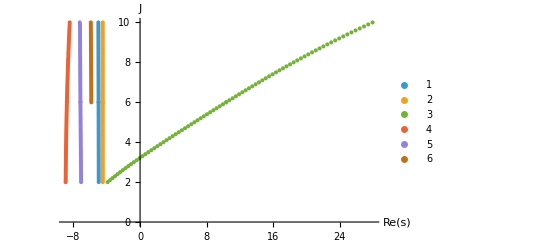

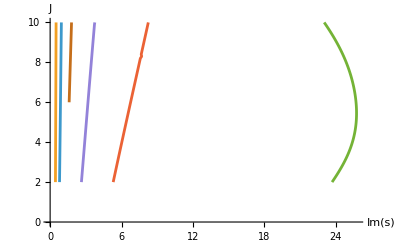

```mathematica
ListPlot[(#[[All]]/. {s_,z_}:>{Re[z],s})&/@allTrajClean,PlotRange->All, AxesLabel->{"Re(s)","J"},PlotLegends->Automatic]
ListPlot[(#[[All]]/. {s_,z_}:>{Im[z],s})&/@allTrajClean,PlotRange->All, AxesLabel->{"Im(s)","J"},Joined->True]
```

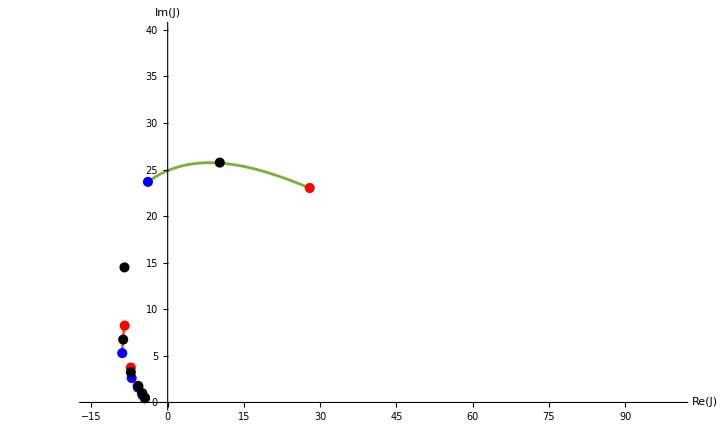

```mathematica
trajPoints=(#[[All]]/. {s_,z_}:>{Re[z],Im[z]})&/@allTrajClean;
starts=First/@trajPoints;
ends=Last/@trajPoints;
ListLinePlot[trajPoints,PlotRange->{{-15,100},{0,40}},AxesLabel->{"Re(J)","Im(J)"},Epilog->{Red,PointSize[0.01],Point[starts],Blue,PointSize[0.01],Point[ends],Black,PointSize[0.01],Point[startPts6d[[All,1;;2]]]}]
```